```mathematica
(* Geometrical efficiency *)
(* Angle detector:*)
d=1.0;
l=2*0.15; (* half the length of the bars *)
w= 0.045; (* width of the scintillators *)
s=0.005; (* spacing between scintillators 0.045 *)
angledet={};
deltaangledet=2ArcTan[w/(2*d)]*180/Pi;
deltaanglespace=2ArcTan[s/(2*d)]*180/Pi;
anglein=5;
Do[
angleout=anglein+deltaangledet;
AppendTo[angledet,{anglein,angleout}];
angleout=angleout+deltaanglespace;
anglein=angleout;
,{i,1,24}
];
angledet
angledet[[12,2]]
```

{{5,7.57788},{7.86435,10.4422},{10.7287,13.3066},{13.5931,16.1709},{16.4574,19.0353},{19.3218,21.8996},{22.1861,24.764},{25.0505,27.6283},{27.9148,30.4927},{30.7792,33.3571},{33.6435,36.2214},{36.5079,39.0858},{39.3722,41.9501},{42.2366,44.8145},{45.1009,47.6788},{47.9653,50.5432},{50.8297,53.4075},{53.694,56.2719},{56.5584,59.1362},{59.4227,62.0006},{62.2871,64.8649},{65.1514,67.7293},{68.0158,70.5937},{70.8801,73.458}}

39.0858

```mathematica
180-angledet[[24,2]]
```

106.542

```mathematica
(* Isotropic neutron distribution *)
det=0;
listalpha={};
Do[
thet=ArcCos[2 Random[]-1];
phy=2 Pi*Random[];
z=d Sin[thet] Cos[phy]/Sqrt[Cos[thet]^2+Sin[thet]^2 Sin[phy]^2];
x2=Sin[thet] Sin[phy];
x3=Cos[thet];
alpha=If[x2≥0 && x3≥0,ArcTan[x2/x3]*180/Pi,
If[x2≥0 && x3<0, 180-ArcTan[x2/(-x3)]*180/Pi,
If[x2<0 && x3<0, 180+ArcTan[x2/x3]*180/Pi,
If[x2<0 && x3>=0, 360-ArcTan[(-x2)/x3]*180/Pi
]
]
]
];
AppendTo[listalpha,alpha];
If[z<l/2 && z>-l/2, 
Do[
If[alpha>angledet[[i,1]]&&alpha≤angledet[[i,2]],
det++];
,{i,1,24}
];
];
(*Print[z," ", alpha];*)
,{j,1,10000}
]
det/10000*100.0
```

2.72

```mathematica
listalpha[]
```

{212.144,79.5595,214.908,101.05,166.222,304.208,132.814,47.6167,331.67,9982,224.864,75.6914,21.5393,346.816,217.772,123.948,102.439,251.096,296.285}[]
 |  |  |  |

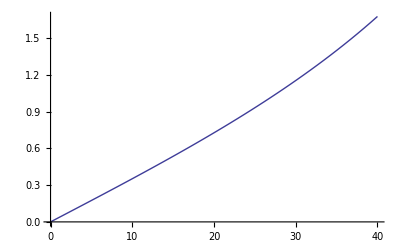

```mathematica
d=2;
Plot[d Tan[th*Pi/180],{th,0,40}]
```

```mathematica
(* calculating the geometrical efficiency *)
d=1;
l=2*0.15; (* half the length of the bars *)
w= 0.045; (* width of the scintillators *)
s=0.045; (* spacing between scintillators *)
effi={};
Do[
r=N[d Tan[the*Pi/180]];
(*Print[the," ",r];*)
eff=0;
Do[
phy=360*Random[];
If[Abs[r Sin[phy*Pi/180]]<l,
Do[
If[
Abs[r Cos[phy*Pi/180]]>s*(det-1)+w*(det-1) && Abs[r Cos[phy*Pi/180]]<s*(det-1)+w*det,eff=eff+1;
]
,{det,1,12,1}
]
];
,{i,1,10000,1}
]
AppendTo[effi,{the,eff}];
,{the,1,40,1}
]
```

```mathematica
effi3=effi;
```

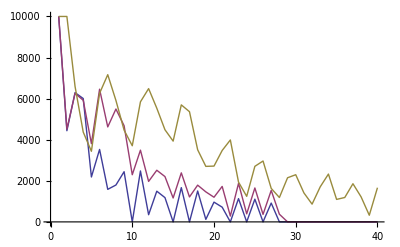

```mathematica
ListPlot[{effi1,effi2,effi3},Joined->True,PlotStyle->Thick]
```

```mathematica
effi1
```

{{1,10000},{2,4438},{3,6292},{4,6005},{5,2186},{6,3527},{7,1584},{8,1795},{9,2443},{10,0},{11,2480},{12,349},{13,1494},{14,1182},{15,0},{16,1668},{17,0},{18,1505},{19,123},{20,962},{21,717},{22,0},{23,1133},{24,0},{25,1106},{26,0},{27,916},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
effi2
```

{{1,10000},{2,4517},{3,6257},{4,5920},{5,3809},{6,6459},{7,4623},{8,5494},{9,4681},{10,2296},{11,3492},{12,1971},{13,2514},{14,2206},{15,1164},{16,2387},{17,1214},{18,1789},{19,1462},{20,1200},{21,1727},{22,285},{23,1874},{24,392},{25,1652},{26,366},{27,1532},{28,374},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}